```mathematica
(*variables and constants*)
Npts=2^19; (*number of points*)(*increased so there's enough ω to get to 2ω0*)
tmin=0;
tmax=400000;
t0=200000.0; (*fs*)
σ=10.0; (*fs*)
A=180337;(*fs^2*)(*goes from 10fs to 100ps*)
Aerf =8300;
Aerfsuper = 7450;
deltat = (tmax-tmin)/Npts; (*the spacing between consecutive time points*)
(*w0 = 2.355; *)
c = 299792458; (*m/s*)
w0 = 2*Pi*c/800 *(10^-6)//N (*units of fs^-1*)
```

2.35456

```mathematica
(*build the original laser pulse in time domain*)
ELaser = Exp[-2*Log[2]*(t-t0)^2/(σ^2)]*Exp[-I*w0*t];
Quiet[PulseLaser = Table[ELaser,{t,tmin,tmax,(tmax-tmin)/(Npts-1)}]];
tlist=Table[t,{t,tmin,tmax,(tmax-tmin)/(Npts-1)}];
test = Fourier[PulseLaser];
```

```mathematica
(*frequency domain*)
freqList=Table[2*Pi*(s-1)/(deltat*Npts),{s,1,Npts}]//N;
maxU = Max[Chop[test*Conjugate[test]]]
testw = ListPlot[Table[{freqList[[i]],test[[i]]*Conjugate[test[[i]]]},{i,1,Length[freqList]}],PlotRange->All, Joined->True,GridLines->{{w0,2.2159380861728284,2.493199345815396},{maxU/2}}]
```

0.000742579

-Graphics-

```mathematica
(*just trying to figure out the width of the spectrum before stretching*)
NearestTo[maxU/2,8][Chop[test*Conjugate[test]]] (*finds the y values closest to the half-max*)
index1 = Position[Chop[test*Conjugate[test]],0.00037128520681567164] (*gives the x index of the y values*)
freqList[[141072]] (*finds the corresponding freq value to the index*)
index2 = Position[Chop[test*Conjugate[test]],0.00037128694537794663]
freqList[[158723]]
FWHMunstretch = 2.493199345815396 - 2.2159380861728284
```

{0.000371287,0.000371285,0.000371344,0.000371345,0.000371229,0.000371227,0.000371402,0.000371404}

{{141072}}

2.21594

{{158723}}

2.4932

0.277261

```mathematica
(*this takes just under 4 mins for 2^19 points*)
(*we need the frequency points ("x values") from the FT*)
freqList=Table[2*Pi*(s-1)/(deltat*Npts),{s,1,Npts}]//N;
(*linear chirp*)
phi[w_]:= A*(w-w0)^2
Quiet[phiList = Table[phi[freqList[[i]]], {i,1,Npts}]];
(*erf chirp*)
x[w_] :=(w-w0)*2*σ/Sqrt[2*Log[256]];
phiErf[w_] := Aerf*((Exp[-x[w]^2]-1)/Sqrt[Pi]+x[w]*Erf[x[w]]) (*WITH the -1*)
Quiet[phiErfList = Table[phiErf[freqList[[i]]], {i,1,Npts}]];
(*super erf chirp*)
xsuper[w_] :=(w-w0)*2*1.12*σ/Sqrt[2*Log[256]];
phiErfsuper[w_] := Aerfsuper*((Exp[-xsuper[w]^2]-1)/Sqrt[Pi]+xsuper[w]*Erf[xsuper[w]])
Quiet[phiErfsuperList = Table[phiErfsuper[freqList[[i]]], {i,1,Npts}]];
```

{0.,0.2,0.4,0.6,0.8,1.}

{2.02327×10^-21,{a1→0.00204363,a2→2.36667×10^-11,T0→-3.81396×10^-16,a3→0.965498,σFWHM→14.1421}}

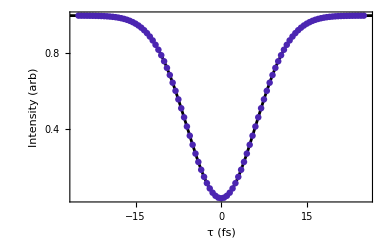

```mathematica
tauList = Table[tau, {tau,-25.,25.,0.5}];
xticks = Table[xt, {xt, 0, 1,0.2}]
fitfunc[t_]:= (a1 - a2*(t-T0)^2)*(1 -a3* Exp[-4*Log[2]*(t-T0)^2/(σFWHM^2)]);
linDip = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\lin_dips_mar7\\dip_0.txt", "List"];
linDipmax = Max[linDip];
Chisq = Sum[(linDip[[i]]-fitfunc[tauList[[i]]])^2,{i,1,Length[tauList]}];
fitvals=FindMinimum[Chisq,{{a1,0.0025},{a2,0.00000001},{T0,0},{a3,0.9},{σFWHM,10}}]
pfit=Quiet[Plot[fitfunc[t]/linDipmax/.{fitvals[[2]]},{t,-300,300},PlotRange->{{-25.5,25.5},All}, PlotStyle->Black, AxesOrigin->{-25.5,0}]];
linDipPlot =ListPlot[Table[{ tauList[[i]],linDip[[i]]/linDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#4B25B1"],PointSize[0.012]}];
Show[pfit,linDipPlot, PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{"τ (fs) ","Intensity (arb)"},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}]
```

{2.08924×10^-10,{a1→0.00305067,a2→8.71563×10^-9,T0→-6.3669×10^-15,a3→0.976513,σFWHM→10.0017}}

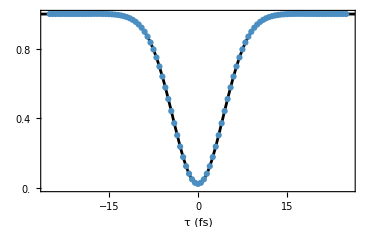

```mathematica
erfDip = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_dips_mar7\\dip_0.txt", "List"];
erfDipmax = Max[erfDip];
Chisq = Sum[(erfDip[[i]]-fitfunc[tauList[[i]]])^2,{i,1,Length[tauList]}];
fitvals=FindMinimum[Chisq,{{a1,0.0025},{a2,0.00000001},{T0,0},{a3,0.9},{σFWHM,10}}]
pfit2=Quiet[Plot[fitfunc[t]/erfDipmax/.{fitvals[[2]]},{t,-300,300},PlotRange->{{-25.5,25.5},{0,1}}, PlotStyle->Black,AxesOrigin->{-25.5,0},Axes->True]];
erfDipPlot =ListPlot[Table[{ tauList[[i]],erfDip[[i]]/erfDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#4B8EC1"],PointSize[0.012]}];
Show[pfit2,erfDipPlot, PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{"τ (fs) "," "},FrameStyle->Directive[Black,14], FrameTicks->{{xticks,True},{True,True}}, FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

{1.55784×10^-8,{a1→0.00310779,a2→6.39408×10^-8,T0→7.33096×10^-15,a3→0.984751,σFWHM→8.69502}}

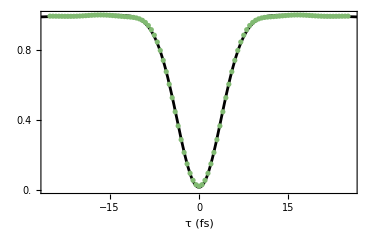

```mathematica
superDip = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_dips_mar7\\dip_0.txt", "List"];
superDipmax = Max[superDip];
Chisq = Sum[(superDip[[i]]-fitfunc[tauList[[i]]])^2,{i,1,Length[tauList]}];
fitvals=FindMinimum[Chisq,{{a1,0.0025},{a2,0.00000001},{T0,0},{a3,0.9},{σFWHM,10}}]
pfit3=Quiet[Plot[fitfunc[t]/superDipmax/.{fitvals[[2]]},{t,-300,300},PlotRange->{{-25.5,25.5},{0,1}}, PlotStyle->Black,AxesOrigin->{-25.5,0}]];
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#81BA72"],PointSize[0.01]}];
Show[pfit3,superDipPlot,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{"τ (fs)"," "},FrameStyle->Directive[Black,14], FrameTicks->{{xticks,True},{True,True}},FrameTicksStyle->{{FontSize->0,Automatic},{Automatic,Automatic}}]
```

```mathematica
(*create the chirped and antichirped pulses*)
PulseLaserw = Fourier[PulseLaser];
Ec = Table[PulseLaserw[[i]]*Exp[I*phiList[[i]]],{i, 1, Npts}]; (*extra term to offset*)
Ea = Table[PulseLaserw[[i]]*Exp[-I*phiList[[i]]],{i, 1, Npts}];
EcErf = Table[PulseLaserw[[i]]*Exp[I*phiErfList[[i]]],{i, 1, Npts}];
EaErf = Table[PulseLaserw[[i]]*Exp[-I*phiErfList[[i]]],{i, 1, Npts}];
EcErfsuper = Table[PulseLaserw[[i]]*Exp[I*phiErfsuperList[[i]]],{i, 1, Npts}];
EaErfsuper = Table[PulseLaserw[[i]]*Exp[-I*phiErfsuperList[[i]]],{i, 1, Npts}];
(*combine chirped and antichirped in the beam splitter*)
E1 = Ec+Ea;
E2 =Ec-Ea;
E1Erf = EcErf+EaErf;
E2Erf =EcErf-EaErf;
E1Erfsuper = EcErfsuper+EaErfsuper;
E2Erfsuper =EcErfsuper-EaErfsuper;
```

```mathematica
(*add the time delay between the pulses*)
tau=100;
(*check the delay in the time domain*)
tdelay[w_]:= Exp[I*w*tau]
tdelayList = Table[tdelay[freqList[[i]]], {i,1,Npts}];
```

```mathematica
(*these blocks take 3.5mins each with 2^19 points*)
(*sum frequency generation in the frequency domain*)
data=Reap[
Do[
tdelayList = Table[tdelay[freqList[[i]]], {i,1,Npts}];
ESFGt = InverseFourier[E1]*InverseFourier[E2*tdelayList];
ESFGw=Fourier[ESFGt];
Sow[Table[ESFGw[[i]]*Conjugate[ESFGw[[i]]],{i,1,Length[freqList]}]]
,{tau,-25.,25.,0.5}]
];
data=data[[2]];
```

```mathematica
dataErf=Reap[
Do[
tdelayList = Table[tdelay[freqList[[i]]], {i,1,Npts}];
ESFGtErf = InverseFourier[E1Erf]*InverseFourier[E2Erf*tdelayList];
ESFGwErf=Fourier[ESFGtErf];
Sow[Table[ESFGwErf[[i]]*Conjugate[ESFGwErf[[i]]],{i,1,Length[freqList]}]]
,{tau,-25.,25.,0.5}]
];
dataErf=dataErf[[2]];
```

```mathematica
dataErfsuper=Reap[
Do[
tdelayList = Table[tdelay[freqList[[i]]], {i,1,Npts}];
ESFGtErfsuper = InverseFourier[E1Erfsuper]*InverseFourier[E2Erfsuper*tdelayList];
ESFGwErfsuper=Fourier[ESFGtErfsuper];
Sow[Table[ESFGwErfsuper[[i]]*Conjugate[ESFGwErfsuper[[i]]],{i,1,Length[freqList]}]]
,{tau,-25.,25.,0.5}]
];
dataErfsuper=dataErfsuper[[2]];
```

```mathematica
(*this stuff is for getting the right numbers on the axes*)
tauList = Table[tau, {tau,-25.,25.,0.5}];
low = 299753;
high =299833;
wRange = high - low;
maxI = Max[Chop[data[[1,2,low;;high]]]]
wMax = (2*Pi*(Npts-1))/tmax;
w0index = (2*w0)*(tmax)/(2*Pi)+1;
deltaw = wMax/Npts //N;
(*labels for ω-ω0 version*)
ytickSpecification=Table[{i,Round[(freqList[[i+(low-1)]]-(2*w0)),0.0001]*10^4},{i,1,wRange+10,20}]
(*labels for λ version*)
ytickSpecification2=Table[{i,Round[2*Pi*c/(freqList[[i+(low-1)]])*10^-6,0.01]},{i,1,wRange+10,20}]
(*x labels*)
xtickSpecification = Table[{i,tauList[[i+1]]},{i,0,Length[tauList],10}];
```

0.000368429

{{1,-6.},{21,-3.},{41,0.},{61,3.},{81,6.}}

{{1,400.05},{21,400.03},{41,400.},{61,399.97},{81,399.95}}

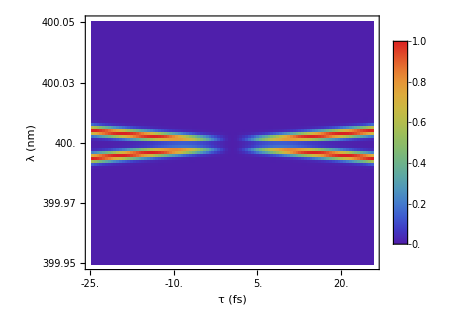

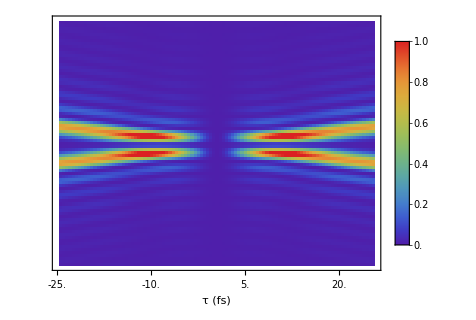

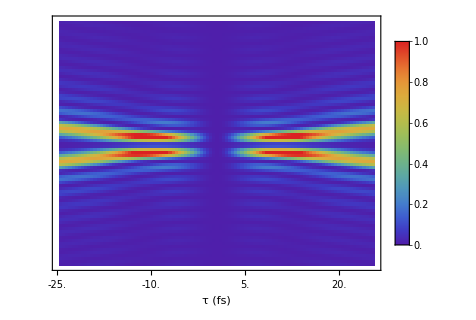

```mathematica
(*normalized Xs*)
MatrixPlot[Transpose[data[[1, All, low;;high]]/maxI], ColorFunction->(ColorData[{"Rainbow",{-0.07,1}}]),ColorFunctionScaling->False, PlotLegends->BarLegend[{Automatic,{0,1}}],FrameTicks->{ytickSpecification2,xtickSpecification},FrameLabel->{{"τ (fs) "," "},{"λ (nm)"," "}},FrameStyle->Directive[Black,12]]
MatrixPlot[Transpose[dataErf[[1, All, low;;high]]/maxI],ColorFunction->(ColorData[{"Rainbow",{-0.07,1}}]),ColorFunctionScaling->False, PlotLegends->BarLegend[{Automatic,{0,1}}],FrameTicks->{False,xtickSpecification},FrameLabel->{{" τ (fs)"," "},{" "," "}},FrameStyle->Directive[Black,12]]
MatrixPlot[Transpose[dataErfsuper[[1, All,  low;;high]]/maxI],ColorFunction->(ColorData[{"Rainbow",{-0.07,1}}]),ColorFunctionScaling->False, PlotLegends->BarLegend[{Automatic,{0,1}},LegendMarkerSize->270],FrameTicks->{False,xtickSpecification},FrameLabel->{{"τ (fs) "," "},{" "," "}}, FrameStyle->Directive[Black,12]]
```

```mathematica
dispXticks2= Table[{i*1000,i},{i,0,64,16}]
testingTicks = Table[{i/0.02232382460030012,i},{i,0,1428,300}]
widthTicks = Table[{i,i},{i,0,800,200}]
```

{{0,0},{16000,16},{32000,32},{48000,48},{64000,64}}

{{0.,0},{13438.6,300},{26877.1,600},{40315.7,900},{53754.2,1200}}

{{0,0},{200,200},{400,400},{600,600},{800,800}}

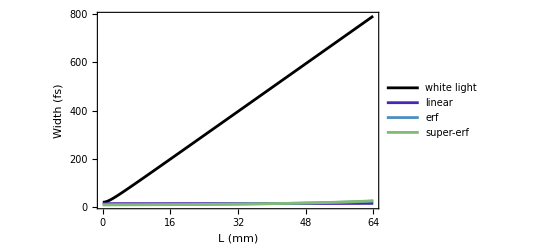

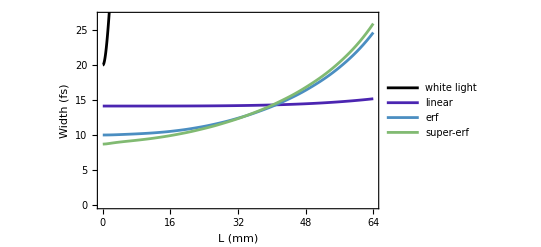

```mathematica
(*dispersion comparison plots*)
lindata = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\linear_0_64_mar7.txt", "CSV"]];
erfdata = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_0_64_mar7.txt", "CSV"]];
erfsuperdata = Transpose[Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_0_64_mar7.txt", "CSV"]];wlicalc = Table[Sqrt[4*σF^2+4*(Log[16])^2ϵ^2/σF^2]/.{σF->10},{ϵ,0,1428}]//N;
Lvalues = Table[ϵ/0.02232382460030012, {ϵ,0,1428}];wli = ListPlot[Table[{Lvalues[[i]],wlicalc[[i]]},{i,1,Length[Lvalues]}],Joined->True,PlotStyle->Black,PlotLegends->{Style["white light",14]}];
linCPI = ListPlot[Table[{ lindata[[1]][[i]],lindata[[2]][[i]]}, {i, 1 , Length[lindata[[1]]]}], PlotRange->{All,All}, Joined->True, PlotStyle->RGBColor["#4B25B1"],PlotLegends->{Style["linear",14]}];
erfCPI = ListPlot[Table[{ erfdata[[1]][[i]],erfdata[[2]][[i]]}, {i, 1 , Length[erfdata[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->RGBColor["#4B8EC1"],PlotLegends->{Style["erf",14]}];
erfsuperCPI = ListPlot[Table[{ erfsuperdata[[1]][[i]],erfsuperdata[[2]][[i]]}, {i, 1 , Length[erfsuperdata[[1]]]}], PlotRange->{All, All}, Joined->True,PlotStyle->RGBColor["#81BA72"],PlotLegends->{Style["super-erf",14]}];
Show[wli, linCPI, erfCPI,erfsuperCPI, PlotRangePadding->{{0.05,0.05},{0,0.5}},PlotRange->{All,All}, Frame-> True,FrameLabel->{{"Width (fs)"," "},{"L (mm)",Row[{"ϵ (",Superscript["fs","2"],")"}]}},FrameStyle->Directive[Black,24],FrameTicks-> {{widthTicks, False},{dispXticks2, testingTicks}}]
Show[wli,linCPI, erfCPI, erfsuperCPI, PlotRangePadding->{{0.5,0.5},{0.1,0.5}},PlotRange->{All,{0,27}},Frame-> True,FrameLabel->{{"Width (fs)"," "},{"L (mm)",Row[{"ϵ (",Superscript["fs","2"],")"}]}},FrameStyle->Directive[Black,10],FrameTicks-> {{Automatic, False},{dispXticks2, testingTicks}}, Axes->False]
```

```mathematica
(*freqList=Table[2*Pi*(s-1)/(deltat*Npts),{s,1,Npts}]//N;*)
(*linear chirp*)
specFWHM = 0.277261;
phi0[w_]:= A*(w-w0)^2
phiList0 = Table[phi0[i], {i,w0-specFWHM*2,w0+specFWHM*2,0.01}];
(*erf chirp*)
x0[w_] :=(w-w0)*2*σ/Sqrt[2*Log[256]];
phiErf0[w_] := Aerf*((Exp[-x0[w]^2]-1)/Sqrt[Pi]+x0[w]*Erf[x0[w]]) (*took out the -1*)
Quiet[phiErfList0 = Table[phiErf0[i], {i,w0-specFWHM*2,w0+specFWHM*2,0.01}]];
```

```mathematica
(*super erf chirp*)
xsuper0[w_] :=(w-w0)*2*1.12*σ/Sqrt[2*Log[256]];
phiErfsuper0[w_] := Aerfsuper*((Exp[-xsuper0[w]^2]-1)/Sqrt[Pi]+xsuper0[w]*Erf[xsuper0[w]])
phiErfsuperList0 = Table[phiErfsuper0[i], {i,w0-specFWHM*2,w0+specFWHM*2,0.01}];
```

```mathematica
(*shifted so that w0=0*)
freqList=Table[2*Pi*(s-1)/(deltat*Npts),{s,1,Npts}]//N;
wVals = Table[i,{i,-specFWHM*2,specFWHM*2,0.01}]; (*add w0 to reshift back to w0*)
LinPhi = ListPlot[Table[{wVals[[i]],phiList0[[i]]},{i, 1, Length[wVals]}],Joined->True, PlotStyle->RGBColor["#4B25B1"],PlotLegends->{Style["linear",12]}];
ErfPhi = ListPlot[Table[{wVals[[i]],phiErfList0[[i]]},{i, 1, Length[wVals]}],Joined->True,PlotStyle->RGBColor["#4B8EC1"],PlotLegends->{Style["erf",12]}];
SuperPhi = ListPlot[Table[{wVals[[i]],phiErfsuperList0[[i]]},{i, 1, Length[wVals]}],Joined->True,PlotStyle->RGBColor["#81BA72"],PlotRange->All,PlotLegends->{Style["super-erf",12]}];
specMax = Max[Chop[test*Conjugate[test]]];
spec = ListPlot[Table[{freqList[[i]]-w0,test[[i]]*Conjugate[test[[i]]]/specMax*4*10^4},{i,149897-2*17651,149897+2*17651}],PlotRange->All, PlotStyle->Black,Joined->True,PlotLegends->{Style["spectral intensity",12]}];
phiYticks= Table[{i,N[i/10000,2]},{i,0,50000,10000}];
phiXticks = Table[{i,i},{i,w0-specFWHM*2,w0+specFWHM*2,0.5}];
specYticks = Table[{i,NumberForm[N[i/(4*10^4)],{2,1}]},{i,0,50000,20000}];
(*Show[spec,LinPhi,ErfPhi,SuperPhi, PlotRange->{All,All},Frame->True,FrameLabel->{{Row[{"ϕ (",Superscript["10","4"],")"}],Row[{"Intensity (arb. units)"}]},{Row[{"ω-",Subscript["ω","0"]," (",Superscript["fs","-1"],")"}]," "}}, FrameTicks-> {{phiYticks, specYticks},{Automatic, None}},FrameStyle->Directive[Black,20], Axes->False]*)
(*Show[ErfPhi,SuperPhi]*)
```

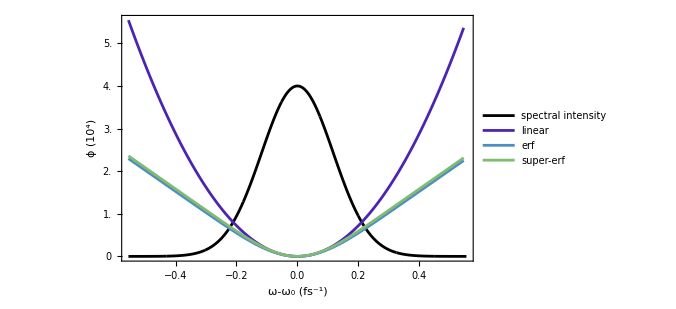

```mathematica
(*smaller font version for side by side*)
Show[spec,LinPhi,ErfPhi, SuperPhi,PlotRange->{All,All},Frame->True,FrameLabel->{{Row[{"ϕ (",Superscript["10","4"],")"}],Row[{"Intensity (arb. units)"}]},{Row[{"ω-",Subscript["ω","0"]," (",Superscript["fs","-1"],")"}]," "}}, FrameTicks-> {{phiYticks, specYticks},{Automatic, None}},PlotRangePadding->{{Automatic,Automatic},{500,500}},FrameStyle->Directive[Black,16], Axes->False]
```

360674 (-2.35456+w)

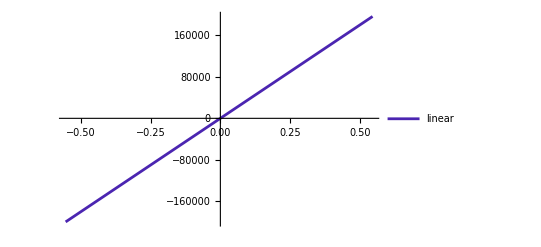

```mathematica
Dlin = D[phi0[w],w]
DphiList0 = Dlin /. w->Table[i,{i,w0-specFWHM*2,w0+specFWHM*2,0.01}];
DlinPlot = ListPlot[Table[{wVals[[i]],DphiList0[[i]]},{i, 1, Length[wVals]}],Joined->True, PlotStyle->{RGBColor["#4B25B1"]},PlotLegends->{Style["linear",12]}]
```

8300 (0.+6.00561 Erf[6.00561 (-2.35456+w)])

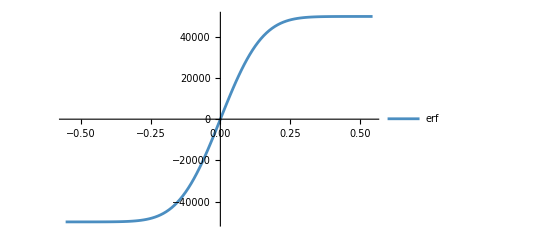

```mathematica
Derf = D[phiErf0[w],w]
DphiErfList0 = Derf /. w->Table[i,{i,w0-specFWHM*2,w0+specFWHM*2,0.01}];
DerfPlot = ListPlot[Table[{wVals[[i]],DphiErfList0[[i]]},{i, 1, Length[wVals]}],Joined->True, PlotStyle->{RGBColor["#4B8EC1"]},PlotLegends->{Style["erf",12]}]
```

7450 (0.+6.72629 Erf[6.72629 (-2.35456+w)])

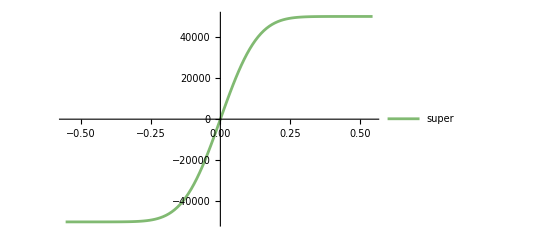

```mathematica
Dsuper = D[phiErfsuper0[w],w]
DphiErfsuperList0 = Dsuper /. w->Table[i,{i,w0-specFWHM*2,w0+specFWHM*2,0.01}];
DerfsuperPlot = ListPlot[Table[{wVals[[i]],DphiErfsuperList0[[i]]},{i, 1, Length[wVals]}],Joined->True, PlotStyle->{RGBColor["#81BA72"]},PlotLegends->{Style["super",12]}]
```

```mathematica
tYticks2= Table[{i,i/1000},{i,-200000,200000,50000}]
phiYticks2= Table[{i,i/10000},{i,-200000,200000,50000}]
specYticks2 = Table[{i,NumberForm[N[i/(4*10^4)],{2,1}]},{i,-80000,80000,40000}]
```

{{-200000,-200},{-150000,-150},{-100000,-100},{-50000,-50},{0,0},{50000,50},{100000,100},{150000,150},{200000,200}}

{{-200000,-20},{-150000,-15},{-100000,-10},{-50000,-5},{0,0},{50000,5},{100000,10},{150000,15},{200000,20}}

{{-80000,-2.0},{-40000,-1.0},{0,0.0},{40000,1.0},{80000,2.0}}

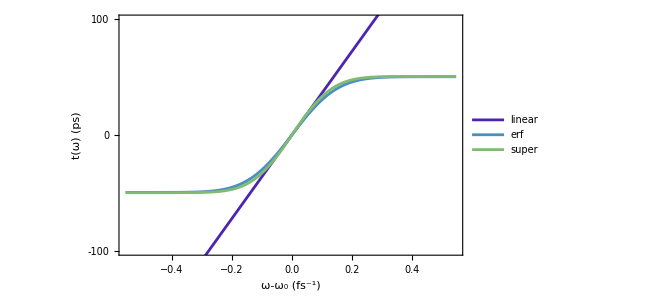

```mathematica
Show[DlinPlot, DerfPlot, DerfsuperPlot, PlotRange->{-100000,99000},PlotRangePadding->{{Automatic,Automatic},{500,500}},Frame->True,FrameLabel->{{Row[{"t(ω) (ps)"}]," "},{Row[{"ω-",Subscript["ω","0"]," (",Superscript["fs","-1"],")"}]," "}}, FrameTicks-> {{tYticks2, Automatic},{Automatic, Automatic}},FrameStyle->Directive[Black,16]]
(*Show[DerfPlot, DerfsuperPlot, Frame->True]*)
```

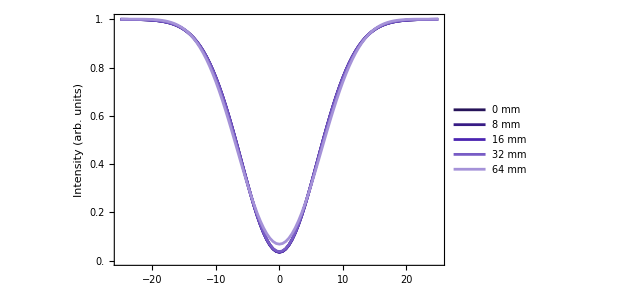

```mathematica
linDipPlot =ListPlot[Table[{ tauList[[i]],linDip[[i]]/linDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#261359"]}, Joined-> True,PlotLegends->{Style["0 mm",20]}];

linDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\lin_dips_mar7\\dip_8000.txt", "List"];
linDipmax2= Max[linDip8mm];
linDipPlot2 =ListPlot[Table[{ tauList[[i]],linDip8mm[[i]]/linDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#381C85"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

linDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\lin_dips_mar7\\dip_16000.txt", "List"];
linDipmax3= Max[linDip16mm];
linDipPlot3 =ListPlot[Table[{ tauList[[i]],linDip16mm[[i]]/linDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#4B25B1"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

linDip32mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\lin_dips_mar7\\dip_32000.txt", "List"];
linDipmax4= Max[linDip32mm];
linDipPlot4 =ListPlot[Table[{ tauList[[i]],linDip32mm[[i]]/linDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#785CC5"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["32 mm",20]}];

linDip64mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\lin_dips_mar7\\dip_64000.txt", "List"];
linDipmax5= Max[linDip64mm];
linDipPlot5 =ListPlot[Table[{ tauList[[i]],linDip64mm[[i]]/linDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A592D8"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["64 mm",20]}];

Show[linDipPlot, linDipPlot2, linDipPlot3, linDipPlot4, linDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity (arb. units)"," "},{" ", " "}},FrameStyle->Directive[Black,24],FrameTicks->{{xticks,True},{True,True}},FrameTicksStyle->{{Automatic,FontSize->0},{FontSize->0,Automatic}}]
```

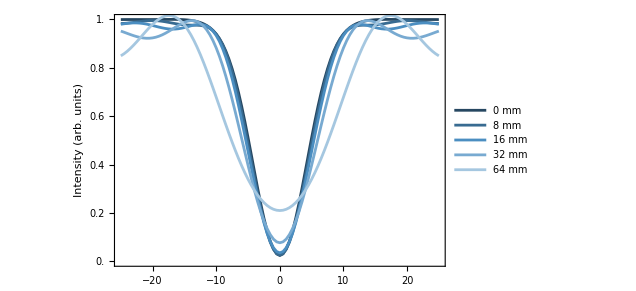

```mathematica
erfDipPlot =ListPlot[Table[{ tauList[[i]],erfDip[[i]]/erfDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#264761"]}, Joined->True,PlotLegends->{Style["0 mm",20]}];

erfDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_dips_mar7\\dip_8000.txt", "List"];
erfDipmax2= Max[erfDip8mm];
erfDipPlot2 =ListPlot[Table[{ tauList[[i]],erfDip8mm[[i]]/erfDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#386B91"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

erfDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_dips_mar7\\dip_16000.txt", "List"];
erfDipmax3= Max[erfDip16mm];
erfDipPlot3 =ListPlot[Table[{ tauList[[i]],erfDip16mm[[i]]/erfDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#4B8EC1"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

erfDip32mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_dips_mar7\\dip_32000.txt", "List"];
erfDipmax4= Max[erfDip32mm];
erfDipPlot4 =ListPlot[Table[{ tauList[[i]],erfDip32mm[[i]]/erfDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#78AAD1"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["32 mm",20]}];

erfDip64mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\erf_dips_mar7\\dip_64000.txt", "List"];
erfDipmax5= Max[erfDip64mm];
erfDipPlot5 =ListPlot[Table[{ tauList[[i]],erfDip64mm[[i]]/erfDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A5C7E0"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["64 mm",20]}];

Show[erfDipPlot, erfDipPlot2, erfDipPlot3, erfDipPlot4, erfDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity (arb. units)"," "},{" ", " "}},FrameStyle->Directive[Black,24],FrameTicks->{{xticks,True},{True,True}},FrameTicksStyle->{{Automatic,FontSize->0},{FontSize->0,Automatic}}]
```

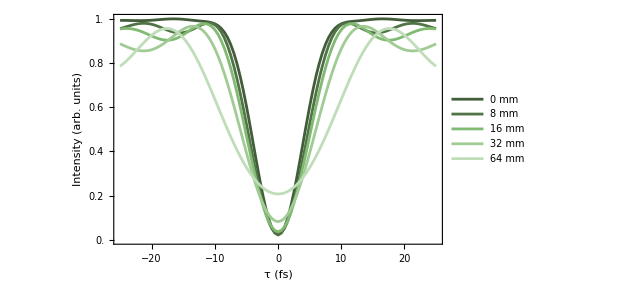

```mathematica
superDipPlot =ListPlot[Table[{ tauList[[i]],superDip[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,PlotStyle->{RGBColor["#415D39"]}, Joined->True,PlotLegends->{Style["0 mm",20]}];

superDip8mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_dips_mar7\\dip_8000.txt", "List"];
superDipmax2= Max[superDip8mm];
superDipPlot2 =ListPlot[Table[{ tauList[[i]],superDip8mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#517447"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "8mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["8 mm",20]}];

superDip16mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_dips_mar7\\dip_16000.txt", "List"];
superDipmax3= Max[superDip16mm];
superDipPlot3 =ListPlot[Table[{ tauList[[i]],superDip16mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#81BA72"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "16mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["16 mm",20]}];

superDip32mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_dips_mar7\\dip_32000.txt", "List"];
superDipmax4= Max[erfDip32mm];
superDipPlot4 =ListPlot[Table[{ tauList[[i]],superDip32mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#A1CB95"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "32mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["32 mm",20]}];

superDip64mm = Import["C:\\Users\\madel\\OneDrive - University of Waterloo\\phys 437B research proj\\new chirps\\Mar7_results\\super_dips_mar7\\dip_64000.txt", "List"];
superDipmax5= Max[superDip64mm];
superDipPlot5 =ListPlot[Table[{ tauList[[i]],superDip64mm[[i]]/superDipmax}, {i, 1 , Length[tauList]}], PlotRange->All,Joined->True,PlotStyle->{RGBColor["#C0DDB9"],PointSize[0.012]},PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity"," "},{"τ (fs) ", "64mm "}},FrameStyle->Directive[Black,14],FrameTicks->{{xticks,True},{True,True}}, Axes->False,PlotLegends->{Style["64 mm",20]}];

Show[superDipPlot, superDipPlot2, superDipPlot3, superDipPlot4, superDipPlot5,Axes->False,PlotRangePadding->{{0.05,0.05},{0,0.08}},Frame->{{True,True},{True,True}},FrameLabel->{{"Intensity (arb. units)"," "},{"τ (fs) ", " "}},FrameStyle->Directive[Black,24], FrameTicks->{{xticks,True},{True,True}},FrameTicksStyle->{{Automatic,FontSize->0},{Automatic,Automatic}}]
```